## Lagrangian for the trebuchet

```mathematica
ClearAll["Global`*"]
```

#### Initial Conditions

```mathematica
Pi/3//N
```

1.0472

```mathematica
Mb=0.045;(*Mass of the bar*)
theta0 = 1;(*This is the angle with respect of the horizontal of the short arm*)
phi0 = 0;(*angle with respect to the vertical of the counterarm*)
Lt=.99;(*Total length of the bar*)
Lb = Lt-Ls;(*Length of the Bar*)
Mp = 0.002;(*Mass of the projectile*)
Mcw = 0.162;(*Mass of the counterweigth*)
Mbase = 0.485;(*Mass of the base*)
Msy = Mbase+Mb+Mcw+Mp;(*Mass of the whole trebuchet*)
g =9.81;
Lcw=.12;(*Length of the counterweigth*)
Ls=.36;(*Length of the small arm*)
```

#### Calculating the potential term

```mathematica
Vo = -Mp*Lb* Sin[theta[t]]*g + (Ls*Sin[theta[t]]-Lcw*Cos[phi[t]])*g*Mcw - 1/2 *Sin[theta[t]]*Mb*g*(Lb-Ls);
```

```mathematica
V = Vo;
```

#### Calculating the kinetic term

```mathematica
xp =- Lb *Cos[theta[t]]+x[t];
yp = - Lb*Sin[theta[t]];
xcw = Ls *Cos[theta[t]]+x[t]+Lcw *Sin[phi[t]];
ycw = Ls *Sin[theta[t] ]-Lcw *Cos[phi[t]];
Ib =1/3 ((Lb^3+Ls^3)/(Lb+Ls))*Mb;
xpd=D[xp,t];
ypd=D[yp,t];
xcwd=D[xcw,t];
ycwd=D[ycw,t];
T=1/2*Mp* (xpd^2+ypd^2)+1/2 *Mcw*(xcwd^2+ycwd^2)+Msy*1/2*x'[t]^2+1/2 *Ib*theta'[t]^2;
```

#### The Lagrangian

```mathematica
L = T-V
```

-1.58922 (-0.12 Cos[phi[t]]+0.36 Sin[theta[t]])+0.0719564 Sin[theta[t]]+0.00224775 theta'[t]^2+0.347 x'[t]^2+0.081 ((0.12 Sin[phi[t]] phi'[t]+0.36 Cos[theta[t]] theta'[t])^2+(0.12 Cos[phi[t]] phi'[t]-0.36 Sin[theta[t]] theta'[t]+x'[t])^2)+0.001 (0.3969 Cos[theta[t]]^2 theta'[t]^2+(0.63 Sin[theta[t]] theta'[t]+x'[t])^2)

#### Euler - Lagrange

```mathematica
EL[q_]:=D[L,q[t]]-D[D[L,q'[t]],t]==0;
```

#### Solved Lagrangian

```mathematica
sol = First[NDSolve[{EL[theta],EL[phi],EL[x],
x[0]==0,
theta[0]==theta0,
phi[0]== phi0,
x'[0]==0,
theta'[0]==0,
phi'[0]==0},{x,theta,phi},{t,0,tmax=10}]]
```

{x→InterpolatingFunction[{{0., 10.}}, <>],theta→InterpolatingFunction[{{0., 10.}}, <>],phi→InterpolatingFunction[{{0., 10.}}, <>]}

#### Plots of the different constraints over time

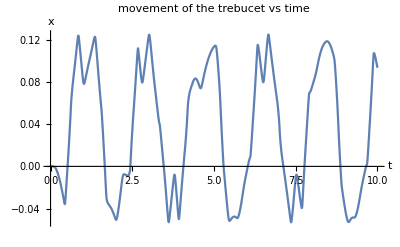

```mathematica
Plot[x[t]/.sol,{t,0,tmax},PlotLabel->"movement of the trebucet vs time",AxesLabel->{t,x}]
```

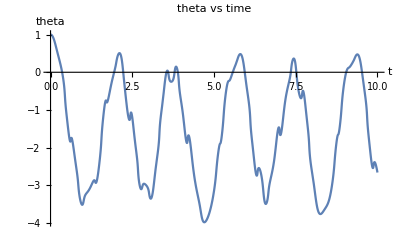

```mathematica
Plot[theta[t]/.sol,{t,0,tmax},PlotLabel->"theta vs time",AxesLabel->{t,theta}]
```

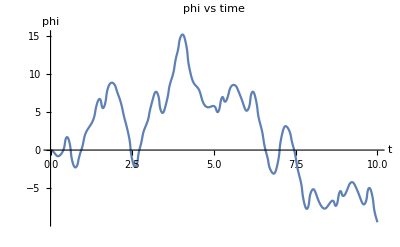

```mathematica
Plot[phi[t]/.sol,{t,0,tmax},PlotLabel->"phi vs time",AxesLabel->{t,phi}]
```

Here are the points of the different parts of the Trebuchet. They are not used in the future code so don’t worry about this

```mathematica
pb1 ={-Lb Cos[theta[t]/.sol]+x[t]/.sol,-Lb Sin[theta[t]/.sol]};(*This is the beginning of the bar*)
pb2 = {Ls Cos[theta[t]/.sol]+x[t]/.sol,Ls Sin[theta[t]/.sol]};(*This is the end of the bar*)
pp = {-Lb Cos[theta[t]/.sol]+x[t]/.sol,-Lb Sin[theta[t]/.sol]}; (*This is the center of the projectile*)
pbcw1={Ls Cos[theta[t]/.sol]+x[t]/.sol,Ls Sin[theta[t]/.sol]};(*This is the beginning of the counterweight arm*) 
pbcw2 ={(Ls Cos[theta[t]/.sol])+(x[t]/.sol)+(Lcw *Sin[phi[t]/.sol]),(Ls Sin[theta[t]/.sol])-(Lcw*Cos[phi[t]/.sol])};(*This is the end or the counterweight arm *)
pcw = {(Ls Cos[theta[t]/.sol])+(x[t]/.sol)+(Lcw *Sin[phi[t]/.sol]),(Ls Sin[theta[t]/.sol])-(Lcw*Cos[phi[t]/.sol])};
```

#### Equations of motion

Here we calculate the position of the projectile as well as the velocity

```mathematica
thetaDer[t_]=D[theta[t]/.sol,t];
```

```mathematica
xder[t_]=D[x[t]/.sol,t];
```

```mathematica
vxpro[t_] :=Lb *Sin[theta[t]/.sol]*thetaDer[t]+xder[t];
```

```mathematica
vypro[t_]:=-Lb*Cos[theta[t]/.sol]*thetaDer[t];
```

```mathematica
xpos[t_] :=-Lb Cos[theta[t]/.sol]+x[t]/.sol
```

```mathematica
ypos[t_]:=-Lb Sin[theta[t]/.sol]
```

```mathematica
thetat[t_]:= theta[t]/.sol
```

#### Velocity over time

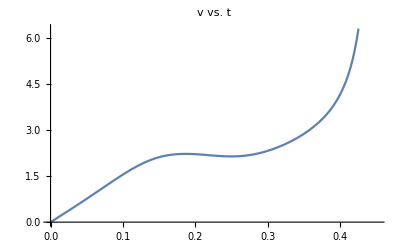

```mathematica
Plot[Sqrt[vxpro[t]^2+vypro[t]^2],{t,0,0.452}, FrameLabel->{"t","v"}, PlotLabel->"v vs. t"]
```

#### Trebuchet Simulation

```mathematica
width=0.215;
height=0.43;
wheelr=0.02;
cwWidth=0.07;
projbox=0.015;
```

```mathematica
Treb=Manipulate[Graphics[{
Thick,Gray,Line[{{xpos[t],ypos[t]},{Ls Cos[theta[t]/.sol]+x[t]/.sol,Ls Sin[theta[t]/.sol]}}],
Brown, Rotate[Rectangle[{xpos[t]-projbox/2,ypos[t]-projbox/2},{xpos[t]+projbox/2,ypos[t]+projbox/2}],thetat[t]],
Thick,Gray, Line[{ 
{(Ls Cos[theta[t]/.sol])+(x[t]/.sol),(Ls Sin[theta[t]/.sol])},
{(Ls Cos[theta[t]/.sol])+(x[t]/.sol)+(Lcw *Sin[phi[t]/.sol]),(Ls Sin[theta[t]/.sol])-(Lcw*Cos[phi[t]/.sol])}
}],
Darker[Green],Rotate[ Rectangle[{(Ls Cos[theta[t]/.sol])+(x[t]/.sol)+(Lcw *Sin[phi[t]/.sol])-cwWidth/2,(Ls Sin[theta[t]/.sol])-(Lcw*Cos[phi[t]/.sol])-cwWidth/2.5},{(Ls Cos[theta[t]/.sol])+(x[t]/.sol)+(Lcw *Sin[phi[t]/.sol])+cwWidth/2,(Ls Sin[theta[t]/.sol])-(Lcw*Cos[phi[t]/.sol])+cwWidth/2.5}],phi[t]/.sol],
Red,Line[{{x[t]/.sol,0},{x[t]-width/2/.sol,-width/2},{x[t]+width/2/.sol,-width/2},{x[t]/.sol,0}}],
Blue,Line[{{x[t]-width/2/.sol,-width/2},{x[t]-width/2/.sol,-width/2-height},{x[t]+width/2/.sol,-width/2-height},{x[t]+width/2/.sol,-width/2}}],
White,Line[{{-0.75,0.7},{-0.75,-(height+width/2+wheelr)},{0.9,-(height+width/2+wheelr)},{0.9,0.7}}],
Black,Circle[{x[t]-width/2/.sol,-width/2-height},wheelr],
Black,Circle[{x[t]+width/2/.sol,-width/2-height},wheelr]
} ,
ImageSize->Large
],
{t,0.0001,2,0.01}]
```